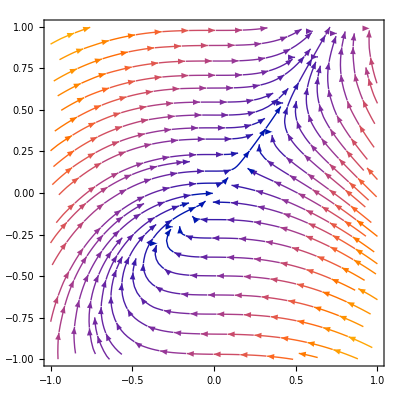

```mathematica
(*2.1a*)
(*Give the index for the fixed point of x=y-x, y=x^2 ​*)
f = y-x;
g = x^2;
p1 = StreamPlot[{f,g}, {x,-1,1}, {y,-1,1}] 
(*Going counterclockwise and using a pen we see that it never does a full rotation -> Idx=0*)
```

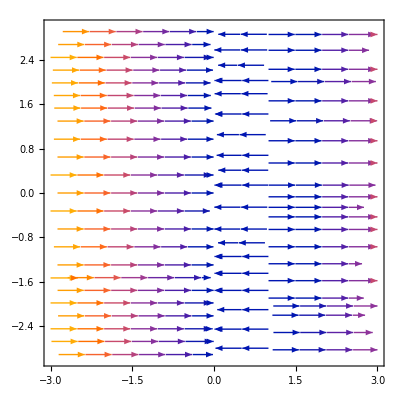

```mathematica
(*2.1b*)
f1 = a*r + r^2;
p2 = StreamPlot[{f1,0}/.a->-1, {r,-3,3}, {θ,-3,3}] 
(*Going counterclockwise and using a pen we see that it does one full rotation
counterclockwise -> Idx=1 *)
```

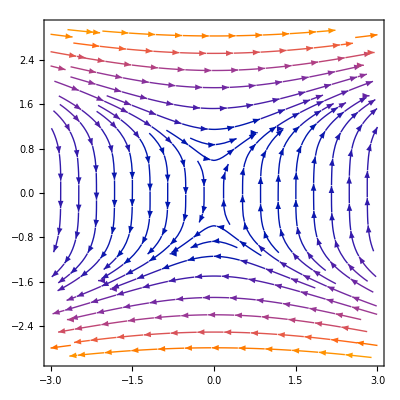

```mathematica
(*2.1c*)
p3 = StreamPlot[{y^3,x}, {x,-3,3}, {y,-3,3}] 
(*Going counterclockwise and using a pen we see that it does one full rotation clockwise -> Idx=-1*)
```

```mathematica
(*2.1d*)
f2[x_, y_] := (x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
g2[x_, y_]:=(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
ϕ[x_,y_] := ArcTan[g2[x,y]/f2[x,y]];

Ic = (Integrate[D[ϕ[1, y], y],{y, -1, 1}]  + Integrate[D[ϕ[x, -1], x],{x, -1, 1}] + Integrate[D[ϕ[-1, y], y],{y, 1, -1}] +Integrate[D[ϕ[x, 1], x],{x, 1, -1}]) / (2*π)
```

n